```mathematica
p1=1/Sqrt[4Pi t]Integrate[Exp[((y-x)^2)/(4t)-y^2],{y,-Infinity,Infinity}]
```

ConditionalExpression[(ⅇ^(x^2/(-1+4 t)))/(√(4-1/t) √t),(4 Re[t]≠1||Re[x/t]>0)&&Re[1/t]<4]

```mathematica
TraditionalForm[p1]
```

ConditionalExpression[(ⅇ^(x^2/(4 t-1)))/(√(4-1/t) √t),(4 Re(t)≠1∨Re(x/t)>0)∧Re(1/t)<4]

```mathematica
TeXForm[p1]
```

\text{ConditionalExpression}\left[\frac{e^{\frac{x^2}{4 t-1}}}{\sqrt{4-\frac{1}{t}} \sqrt{t}},\left(4
   \Re(t)\neq 1\lor \Re\left(\frac{x}{t}\right)>0\right)\land \Re\left(\frac{1}{t}\right)<4\right]

```mathematica
p2=Integrate[Exp[(x-y)/(4t)-y^2],{y,x,Infinity}]
```

1/2 ⅇ^((1+16 t x)/(64 t^2)) √π Erfc[1/(8 t)+x]

```mathematica
u[x_,t_]=Piecewise[{{(p1),t>0},{Exp[-x^2],t==0}}]
```

ConditionalExpression[Piecewise[{{(ⅇ^(x^2/(-1+4 t)))/(√(4-1/t) √t), t>0}, {ⅇ^(-x^2), t==0}, {0, True}}],!(t>0&&!((4 Re[t]≠1||Re[x/t]>0)&&Re[1/t]<4))]

```mathematica
u[x,0]
```

ⅇ^(-x^2)

```mathematica
Plot3D[u[x,t],{x,-10,10},{t,0,10}]
```

-Graphics3D-

```mathematica
Manipulate[Plot[u[x,t],{x,-10,10},PlotRange->{0,1}],{t,0,10}]
```

```mathematica
DSolve[{D[u[x,t],{x,2}]==D[u[x,t],t],u[x,0]==Exp[-x^2]},u,{x,t}]
```

DSolve[{u^(2,0)[x,t]==u^(0,1)[x,t],u[x,0]==ⅇ^(-x^2)},u,{x,t}]

```mathematica
Manipulate[Plot[Exp[-Abs[x-y]/(4t)-y^2],{y,-3,3}],{x,-3,3},{t,0,3}]
```

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i.

```mathematica
u1[x_,t_]:=1/Sqrt[1+4t]Exp[-x^2/(1+4t)]
```

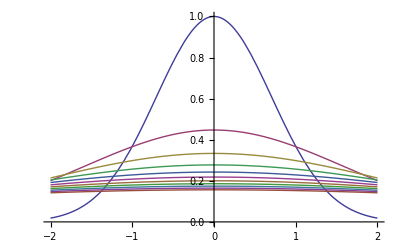

```mathematica
Plot[Evaluate[Table[u1[x,t],{t,0,10}]],{x,-2,2},PlotRange->{0,1}]
```